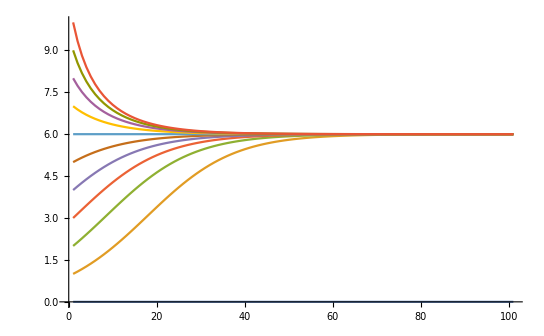

```mathematica
LogisticGrowth[x0_]:=With[{dt=0.1,nSteps=100,r=1,K=6},
f[x_]:=r x(1-x/K);
NestList[#+f[#] dt&,x0,nSteps]
];
ListLinePlot[Table[LogisticGrowth[x0],{x0,0,10}],PlotRange->Full]
```